## MAE 280 B - Linear Control Design Mauricio de Oliveira LQG Control

```mathematica
Hyperlink["http://fccr.ucsd.edu/~mauricio/courses/mae280b"]
```

## Problem Data

```mathematica
m = 100. (* 100 kg *);
r = 300. 10^3 (* 300 km *);
R0 = 6.37 10^6 (* 6.37 10^3 km *);
G = 6.673 10^-11 (* 6.673 N m^2/kg^2 *);
M = 5.98 10^24 (* 5.98 10^24 kg *);
```

Gravitational force constant

```mathematica
k = G M;
```

Angular velocity (rad/s)

```mathematica
ω = Sqrt[k/((R0+r)^3)]
```

0.00115964

“Ground” velocity (m/s)

```mathematica
v = ω*(R0+r)
```

7734.78

### Linearized System Realization

```mathematica
A = {
{0,0,1,0},
{0,0,0,1},
{3 ω^2,0,0,2(r+R0)ω},
{0,0,(-2ω)/(r+R0),0}
};
Bu = {
{0,0},
{0,0},
{1/m,0},
{0,1/(m(r+R0))}
};
Cy={
{1,0,0,0},
{0,r+R0,0,0}
};
Dyu=ConstantArray[0,{2,2}];
```

### Add noise input

```mathematica
Bw=Bu;
Dyw=ConstantArray[0,{2,2}];
```

```mathematica
BB=ArrayFlatten[{{Bu,Bw}}];
DD=ArrayFlatten[{{Dyu,Dyw}}];
```

```mathematica
linearizedSystem=StateSpaceModel[{A,BB,Cy,DD}]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
4.03428×10^-6 | 0 | 0 | 15469.6 | 0.01 | 0 | 0.01 | 0
0 | 0 | -3.47718×10^-10 | 0 | 0 | 1.49925×10^-9 | 0 | 1.49925×10^-9
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6.67×10^6 | 0 | 0 | 0 | 0 | 0 | 0)_^𝒮

### Scaling

Apply similarity transformation

```mathematica
T = DiagonalMatrix[{1,r+R0,1,r+R0}];
```

```mathematica
transformedLinearizedSystem=StateSpaceTransform[linearizedSystem,Inverse[T]]
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0.01 | 0. | 0.01 | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0.01 | 0. | 0.01
1. | 0. | 0. | 0. | 0 | 0 | 0 | 0
0. | 1. | 0. | 0. | 0 | 0 | 0 | 0)_^𝒮

## SISO LQG Design (tangential control + θ measurement)

```mathematica
tanPlusThetaSystem=SystemsModelExtract[transformedLinearizedSystem,{2,3,4},2];
```

```mathematica
sisoSystem=SystemsModelExtract[tanPlusThetaSystem,1,1];
```

```mathematica
Map[ColumnForm,TransferFunctionPoles[sisoSystem],2]
```

{0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ}

```mathematica
Map[ColumnForm,TransferFunctionZeros[sisoSystem],2]
```

{-0.00200855
0.00200855}

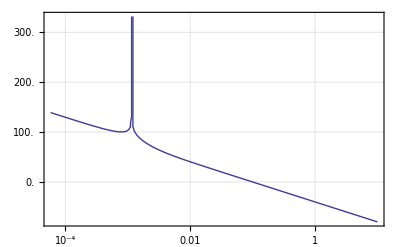
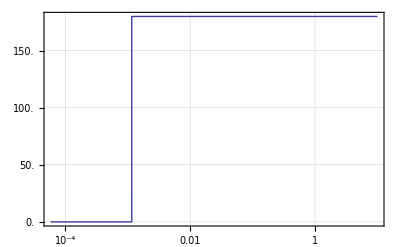

```mathematica
BodePlot[sisoSystem,GridLines->Automatic,PlotLayout->"List"]
```

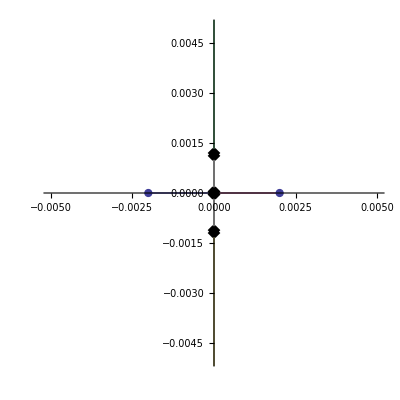

```mathematica
Clear[k]
SystemsModelSeriesConnect[TransferFunctionModel[k],sisoSystem];
RootLocusPlot[%,{k,0,1},PlotRange->{-0.005,0.005}]
```

### Two Riccati Equations Solution

```mathematica
{AA,BB,CC,DD}=Normal[tanPlusThetaSystem];
```

```mathematica
BBu=BB[[All,{1}]];
BBw=BB[[All,{2,3}]];
```

```mathematica
DDyu=DD[[All,{1}]];
DDyw=DD[[All,{2,3}]];
```

#### State - feedback

```mathematica
ρ=1;
Q=IdentityMatrix[4];
R=ρ IdentityMatrix[1];
```

```mathematica
KK=-LQRegulatorGains[StateSpaceModel[{AA,BBu}],{Q,R}];
MatrixForm[KK]
```

(-2.05011 | 1. | -890.798 | -14.6356)

#### State Estimation

```mathematica
Ww=0.1IdentityMatrix[2];
```

```mathematica
Wv=0.1IdentityMatrix[1];
```

```mathematica
FF=-Transpose[LQRegulatorGains[StateSpaceModel[{Transpose[AA],Transpose[CC]}],{BBw.Ww.Transpose[BBw],Wv}]];
MatrixForm[FF]
```

(8.90727
-0.146003
0.0201612
-0.0106584)

#### Controller

```mathematica
sisoController=StateSpaceModel[{AA+BBu.KK+FF.CC,-FF,KK}]
```

(0. | 8.90727 | 1. | 0. | -8.90727
0. | -0.146003 | 0. | 1. | 0.146003
4.03428×10^-6 | 0.0201612 | 0. | 0.00231928 | -0.0201612
-0.0205011 | -0.000658421 | -8.9103 | -0.146356 | 0.0106584
-2.05011 | 1. | -890.798 | -14.6356 | 0)_^𝒮

### LQG solution

```mathematica
LQGRegulator[{tanPlusThetaSystem,1,1},{Ww,Wv},{Q,R}]
```

(0. | 8.90727 | 1. | 0. | -8.90727
0. | -0.146003 | 0. | 1. | 0.146003
4.03428×10^-6 | 0.0201612 | 0. | 0.00231928 | -0.0201612
-0.0205011 | -0.000658421 | -8.9103 | -0.146356 | 0.0106584
2.05011 | -1. | 890.798 | 14.6356 | 0.)_^𝒮

### Closed - loop Analysis

#### Add v component

```mathematica
BBwv=ArrayFlatten[{{BBw,ConstantArray[0,{4,1}]}}];
DDwv=ArrayFlatten[{{ConstantArray[0,{1,2}],IdentityMatrix[1]}}];
W=ArrayFlatten[{{Ww,0},{0,Wv}}];
```

```mathematica
BBwv.W.Transpose[DDwv]
DDwv.W.Transpose[DDwv]
```

{{0.},{0.},{0.},{0.}}

{{0.1}}

#### Compute Cz and Dzu

```mathematica
Cz=ArrayFlatten[{{MatrixPower[Q,1/2]},{ConstantArray[0,{1,4}]}}];
Dzu=ArrayFlatten[{{ConstantArray[0,{4,1}]},{MatrixPower[R,1/2]}}];
```

```mathematica
Transpose[Cz].Dzu
Transpose[Dzu].Dzu
```

{{0},{0},{0},{0}}

{{1}}

#### Closed - loop data

```mathematica
Acl=ArrayFlatten[{{AA,BBu.KK},{-FF.CC,AA+BBu.KK+FF.CC}}];
Bcl=ArrayFlatten[{{BBwv},{-FF.DDwv}}];
Ccl=ArrayFlatten[{{Cz,Dzu.KK}}];
```

```mathematica
Eigenvalues[Acl]//ColumnForm
```

-0.0708588+0.0705623 ⅈ
-0.0708588-0.0705623 ⅈ
-0.0706822+0.0707392 ⅈ
-0.0706822-0.0707392 ⅈ
-0.00347891+6.67396×10^-8 ⅈ
-0.00347891-6.67396×10^-8 ⅈ
-0.00115964+3.22282×10^-8 ⅈ
-0.00115964-3.22282×10^-8 ⅈ

#### Cost through Controllability Gramian

```mathematica
X=LyapunovSolve[Transpose[Acl],-Transpose[Ccl].Ccl];
Tr[Bcl.W.Transpose[Bcl].X]
```

33463.3

#### State covariance matrix

```mathematica
Y=LyapunovSolve[Acl,-Bcl.W.Transpose[Bcl]];
Tr[Transpose[Ccl].Ccl.Y]
```

33463.3

```mathematica
Sqrt[Tr[Y,List]]
```

{66.7338,168.948,0.233742,2.11671,46.9814,168.948,0.213171,2.11668}

#### Frequency - domain

```mathematica
BodePlot[sisoSystem,GridLines->Automatic,PlotLayout->"List"]
```

{-Graphics-,-Graphics-}

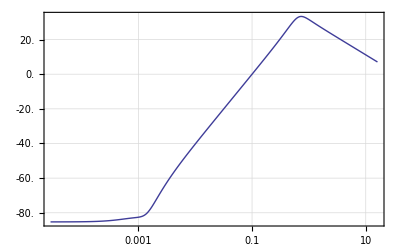
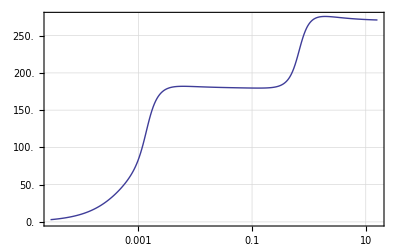

```mathematica
BodePlot[sisoController,GridLines->Automatic,PlotLayout->"List"]
```

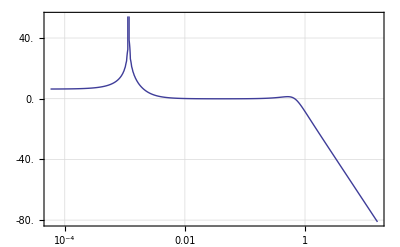
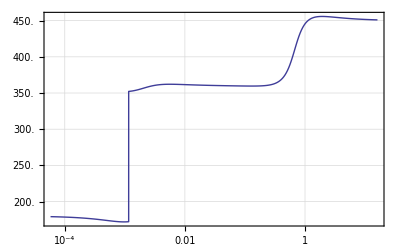

```mathematica
G=SystemsModelSeriesConnect[sisoController,sisoSystem];BodePlot[G,GridLines->Automatic,PlotLayout->"List"]
```

```mathematica
Map[ColumnForm,TransferFunctionPoles[G],2]
```

{-0.803563
-0.00202713
0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ
0.256616-0.623427 ⅈ
0.256616+0.623427 ⅈ}

```mathematica
Map[ColumnForm,TransferFunctionZeros[G],2]
```

{-0.00162848-0.00100088 ⅈ
-0.00162848+0.00100088 ⅈ
0.
0.
0.00156418}

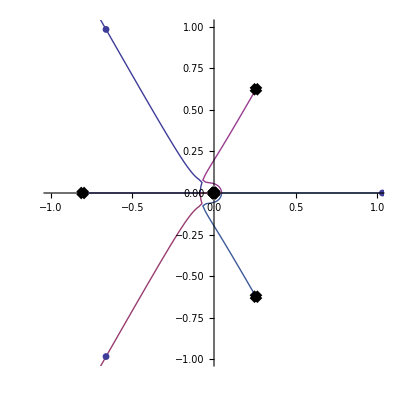

```mathematica
Clear[k]
SystemsModelSeriesConnect[TransferFunctionModel[-k],G];
RootLocusPlot[%,{k,0,10},PlotRange->{-1,1},PlotPoints->500]
```

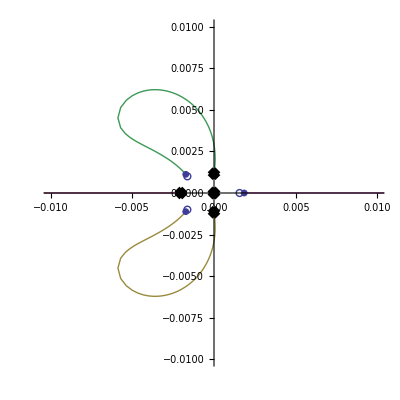

```mathematica
Clear[k]
SystemsModelSeriesConnect[TransferFunctionModel[-k],G];
RootLocusPlot[%,{k,0,10},PlotRange->{-.01,.01},PlotPoints->100]
```

## MIMO LQG Design (tangential/radial control + r/θ measurement)

### Two Riccati Equations Solution

```mathematica
{AA,BB,CC,DD}=Normal[transformedLinearizedSystem];
```

```mathematica
BBu=BB[[All,{1,2}]];
BBw=BB[[All,{3,4}]];
```

```mathematica
DDyu=DD[[All,{1,2}]];
DDyw=DD[[All,{3,4}]];
```

#### State - feedback

```mathematica
ρ=1;
Q=IdentityMatrix[4];
R=ρ IdentityMatrix[2];
```

```mathematica
KK=-LQRegulatorGains[StateSpaceModel[{AA,BBu}],{Q,R}];
MatrixForm[KK]
```

(-1.00027 | 0.0163595 | -14.1793 | -0.0000232767
-0.0163595 | -0.999866 | -0.0000232767 | -14.1765)

#### State Estimation

```mathematica
Ww=0.1IdentityMatrix[2];
```

```mathematica
Wv=0.1IdentityMatrix[2];
```

```mathematica
FF=-Transpose[LQRegulatorGains[StateSpaceModel[{Transpose[AA],Transpose[CC]}],{BBw.Ww.Transpose[BBw],Wv}]];
MatrixForm[FF]
```

(-0.14144 | 2.33931×10^-7
2.33931×10^-7 | -0.141412
-0.0100027 | -0.00016397
0.000164036 | -0.00999866)

#### Controller

```mathematica
mimoController=StateSpaceModel[{AA+BBu.KK+FF.CC,-FF,KK}]
```

(-0.14144 | 2.33931×10^-7 | 1. | 0. | 0.14144 | -2.33931×10^-7
2.33931×10^-7 | -0.141412 | 0. | 1. | -2.33931×10^-7 | 0.141412
-0.0200014 | -3.75314×10^-7 | -0.141793 | 0.00231904 | 0.0100027 | 0.00016397
4.41468×10^-7 | -0.0199973 | -0.00231951 | -0.141765 | -0.000164036 | 0.00999866
-1.00027 | 0.0163595 | -14.1793 | -0.0000232767 | 0 | 0
-0.0163595 | -0.999866 | -0.0000232767 | -14.1765 | 0 | 0)_^𝒮

### LQG solution

```mathematica
LQGRegulator[{transformedLinearizedSystem,{1,2},{1,2}},{Ww,Wv},{Q,R}]
```

(-0.14144 | 2.33931×10^-7 | 1. | 0. | 0.14144 | -2.33931×10^-7
2.33931×10^-7 | -0.141412 | 0. | 1. | -2.33931×10^-7 | 0.141412
-0.0200014 | -3.75314×10^-7 | -0.141793 | 0.00231904 | 0.0100027 | 0.00016397
4.41468×10^-7 | -0.0199973 | -0.00231951 | -0.141765 | -0.000164036 | 0.00999866
1.00027 | -0.0163595 | 14.1793 | 0.0000232767 | 0. | 0.
0.0163595 | 0.999866 | 0.0000232767 | 14.1765 | 0. | 0.)_^𝒮

### Closed - loop Analysis

#### Add v component

```mathematica
BBwv=ArrayFlatten[{{BBw,ConstantArray[0,{4,2}]}}];
DDwv=ArrayFlatten[{{ConstantArray[0,{2,2}],IdentityMatrix[2]}}];
W=ArrayFlatten[{{Ww,0},{0,Wv}}];
```

```mathematica
BBwv.W.Transpose[DDwv]
DDwv.W.Transpose[DDwv]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{{0.1,0.},{0.,0.1}}

#### Compute Cz and Dzu

```mathematica
Cz=ArrayFlatten[{{MatrixPower[Q,1/2]},{ConstantArray[0,{2,4}]}}];
Dzu=ArrayFlatten[{{ConstantArray[0,{4,2}]},{MatrixPower[R,1/2]}}];
```

```mathematica
Transpose[Cz].Dzu
Transpose[Dzu].Dzu
```

{{0,0},{0,0},{0,0},{0,0}}

{{1,0},{0,1}}

#### Closed - loop data

```mathematica
Acl=ArrayFlatten[{{AA,BBu.KK},{-FF.CC,AA+BBu.KK+FF.CC}}];
Bcl=ArrayFlatten[{{BBwv},{-FF.DDwv}}];
Ccl=ArrayFlatten[{{Cz,Dzu.KK}}];
```

```mathematica
Eigenvalues[Acl]//ColumnForm
```

-0.0708954+0.071691 ⅈ
-0.0708954-0.071691 ⅈ
-0.070713+0.0718679 ⅈ
-0.070713-0.0718679 ⅈ
-0.0707131+0.0695487 ⅈ
-0.0707131-0.0695487 ⅈ
-0.0708839+0.0693717 ⅈ
-0.0708839-0.0693717 ⅈ

#### Cost through Controllability Gramian

```mathematica
X=LyapunovSolve[Transpose[Acl],-Transpose[Ccl].Ccl];
Tr[Bcl.W.Transpose[Bcl].X]
```

0.170221

```mathematica
Eigenvalues[X]
```

{8584.87,8580.59,654.793,654.637,20.1673,20.1629,2.80269,2.8025}

#### State covariance matrix

```mathematica
Y=LyapunovSolve[Acl,-Bcl.W.Transpose[Bcl]];
Tr[Transpose[Ccl].Ccl.Y]
```

0.170221

```mathematica
Sqrt[Tr[Y,List]]
```

{0.230342,0.230291,0.0157269,0.0157249,0.197265,0.197213,0.0102897,0.0102879}

```mathematica
Eigenvalues[Y]
```

{0.0855647,0.0855219,0.00653137,0.00652981,0.000200452,0.000200409,0.0000278309,0.000027829}

#### Frequency - domain

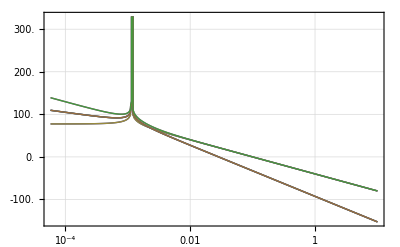
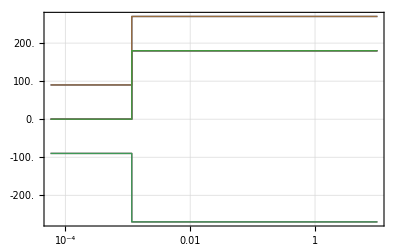

```mathematica
BodePlot[transformedLinearizedSystem,GridLines->Automatic,PlotLayout->"List"]
```

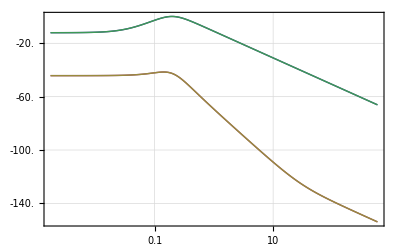
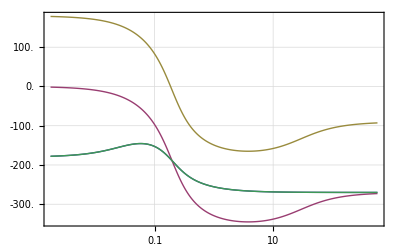

```mathematica
BodePlot[mimoController,GridLines->Automatic,PlotLayout->"List"]
```

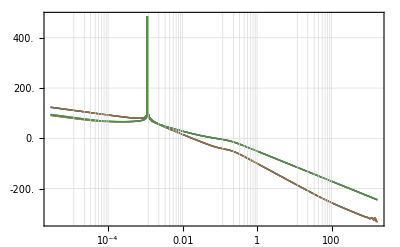
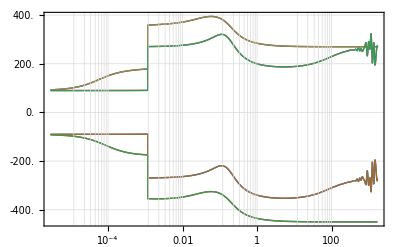

```mathematica
G=SystemsModelSeriesConnect[transformedLinearizedSystem,mimoController];BodePlot[G,GridLines->Automatic,PlotLayout->"List"]
```

```mathematica
GG=SystemsModelExtract[TransferFunctionModel[G],{1,2},{1,2}]
```

((-2.28321×10^-10 s-4.00715×10^-6 s^2-0.000141768 s^3+0.000701999 s^4+0.0198543 s^5+0.160313 s^6+0.566411 s^7+s^8-1. (2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8))/(2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8) | (-9.299×10^-9 s-2.28272×10^-7 s^2-2.29897×10^-6 s^3+0.00159448 s^4+0.0226873 s^5+0.160313 s^6+0.566411 s^7+s^8-1. (2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8))/(2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8)
(9.28775×10^-9 s+2.32427×10^-7 s^2+2.35887×10^-6 s^3+0.00161427 s^4+0.0226875 s^5+0.160313 s^6+0.566411 s^7+s^8-1. (2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8))/(2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8) | (3.43464×10^-10 s-3.99825×10^-6 s^2-0.000141682 s^3+0.000702484 s^4+0.019856 s^5+0.160313 s^6+0.566411 s^7+s^8-1. (2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8))/(2.15721×10^-9 s^2+3.05081×10^-8 s^3+0.00160438 s^4+0.0226874 s^5+0.160313 s^6+0.566411 s^7+s^8))_^𝒯

```mathematica
Map[ColumnForm,TransferFunctionPoles[GG],2]
```

{-0.141606-0.142583 ⅈ
-0.141606+0.142583 ⅈ
-0.1416-0.140264 ⅈ
-0.1416+0.140264 ⅈ
0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ
-0.141606-0.142583 ⅈ
-0.141606+0.142583 ⅈ
-0.1416-0.140264 ⅈ
-0.1416+0.140264 ⅈ
0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ,-0.141606-0.142583 ⅈ
-0.141606+0.142583 ⅈ
-0.1416-0.140264 ⅈ
-0.1416+0.140264 ⅈ
0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ
-0.141606-0.142583 ⅈ
-0.141606+0.142583 ⅈ
-0.1416-0.140264 ⅈ
-0.1416+0.140264 ⅈ
0.
0.
0.-0.00115964 ⅈ
0.+0.00115964 ⅈ}

```mathematica
Map[ColumnForm,TransferFunctionZeros[GG],2]
```

{-0.141593-0.141408 ⅈ
-0.141593+0.141408 ⅈ
-0.0352681
-0.000057063
0.
-85.342
-0.0942111
-0.0707805-0.0706523 ⅈ
-0.0707805+0.0706523 ⅈ
0.,-85.2562
-0.0941574
-0.0707977-0.0706182 ⅈ
-0.0707977+0.0706182 ⅈ
0.
-0.14162-0.141425 ⅈ
-0.14162+0.141425 ⅈ
-0.0353785
0.
0.0000855977}

```mathematica
TransferFunctionCancel[TransferFunctionModel[GG]]
```

(-(0.0028331 (0.000057063+s) (0.0352681+s) ((0.141593-0.141408 ⅈ)+s) ((0.141593+0.141408 ⅈ)+s))/(s ((0.-0.00115964 ⅈ)+s) ((0.+0.00115964 ⅈ)+s) ((0.1416-0.140264 ⅈ)+s) ((0.1416+0.140264 ⅈ)+s) ((0.141606-0.142583 ⅈ)+s) ((0.141606+0.142583 ⅈ)+s)) | -(1.15638×10^-7 ((0.0707805-0.0706523 ⅈ)+s) ((0.0707805+0.0706523 ⅈ)+s) (0.0942111+s) (85.342+s))/(s ((0.-0.00115964 ⅈ)+s) ((0.+0.00115964 ⅈ)+s) ((0.1416-0.140264 ⅈ)+s) ((0.1416+0.140264 ⅈ)+s) ((0.141606-0.142583 ⅈ)+s) ((0.141606+0.142583 ⅈ)+s))
(1.15708×10^-7 ((0.0707977-0.0706182 ⅈ)+s) ((0.0707977+0.0706182 ⅈ)+s) (0.0941574+s) (85.2562+s))/(s ((0.-0.00115964 ⅈ)+s) ((0.+0.00115964 ⅈ)+s) ((0.1416-0.140264 ⅈ)+s) ((0.1416+0.140264 ⅈ)+s) ((0.141606-0.142583 ⅈ)+s) ((0.141606+0.142583 ⅈ)+s)) | -(0.00283139 (-0.0000855977+s) (0.0353785+s) ((0.14162-0.141425 ⅈ)+s) ((0.14162+0.141425 ⅈ)+s))/(s ((0.-0.00115964 ⅈ)+s) ((0.+0.00115964 ⅈ)+s) ((0.1416-0.140264 ⅈ)+s) ((0.1416+0.140264 ⅈ)+s) ((0.141606-0.142583 ⅈ)+s) ((0.141606+0.142583 ⅈ)+s)))_^𝒯